## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PFK1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PFK1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= 
importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 110.7 | 108.1
113.3 | 1/s | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 | 
1 | Kic | adp | 0.0002 | 0.00019
0.00021 |  | Competitive | atp | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | adp | 0.000025 | 0.00002375
0.00002625 |  |  | M | 8.5 | 28 | tris | 0.05 | 
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  |  | 8.5 | 28 | tris | 0.05 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = {1};
kcatPriorities = {1};
inhibitionPriorities={1,0};
activationPriorities = {0,1};
otherParamsPriorities = {1,1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 110.7 | 108.1
113.3 | 1/s | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  |  | 8.5 | 28 | tris | 0.05 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
rxn
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

```mathematica
(*enz ="E_PFK1[c]"
substrateList ={"atp","f6p"};
productList={"fdp", "atp"};
nActiveSites = 1;
bindingReversibility = " <=> ";
releaseReversibility = " <=> ";
transitionReversibility = " <=> ";

catalyticBranch =generateOrderedMechanism[enz, substrateList,  productList, nActiveSites, bindingReversibility, 
						transitionReversibility, releaseReversibility] ;*)


catalyticBranch={"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp",
				"E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp",
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["gdp","c"]},ActivationSites->4,Inhibitors->{m["pep","c"]},InhibitionSites->4];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p
E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp
E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp
E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]
E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$3,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$3,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK13$3,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$3,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$7,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$7,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c))^PFK13$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$7,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$8,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$8,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c))^PFK13$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$8,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$10,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$10,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$10,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$10,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$15,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$21,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,Overscript[(PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c, PFK12],((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,Overscript[(PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c, PFK14],((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15};
catalyticReactionsSet2 ={Overscript[(PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c), PFK11$24],Overscript[(PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c, PFK12$24],Overscript[(PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c), PFK13$24],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c, PFK14$24],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c), PFK15$24]};

catalyticReactionsSet3 ={Overscript[(PFK1^c)_^(gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c), PFK11$25],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c)+fdp^c, PFK12$25],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c), PFK13$25],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c)+adp^c, PFK14$25],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c), PFK15$25]};

catalyticReactionsSet4 ={Overscript[(PFK1^c)_^(gdp^c gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c), PFK11$26],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c gdp^c)+fdp^c, PFK12$26],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c), PFK13$26],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c)+adp^c, PFK14$26],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c), PFK15$26]};
catalyticReactionsSet5 ={Overscript[(PFK1^c)_^(gdp^c gdp^c gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK11$27],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c gdp^c gdp^c)+fdp^c, PFK12$27],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK13$27],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c gdp^c)+adp^c, PFK14$27],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK15$27]};
catalyticReactionsSetsList = {catalyticReactionsSet1,catalyticReactionsSet2,catalyticReactionsSet3,catalyticReactionsSet4,catalyticReactionsSet5};
```

### Setup King-Altman Equations

```mathematica
deleteDirectoryContents[inputPath];
```

#### Define some parameters

```mathematica
MWCFlag=True;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={(*{"prod_inhib_adp",fdp^c->0}*)};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,{(*inhibitionList[[2]])*)}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{atp^c→0,f6p^c→0}

{adp^c→0,fdp^c→0}

{atp^c→∞,f6p^c→∞}

{adp^c→∞,fdp^c→∞}

Added inhibition reactions:

{((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$15,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$21,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

Generating flux equation...

{((PFK1^c&f6p^c&atp^c)_^-((PFK1^c&fdp^c&adp^c)_^)/K_PFK15) Volume_c k_PFK15^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^c))/K_PFK15$3) Volume_c k_PFK15$3^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))/K_PFK15$7) Volume_c k_PFK15$7^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))/K_PFK15$8) Volume_c k_PFK15$8^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))/K_PFK15$10) Volume_c k_PFK15$10^⟶}

Volume_c (-(PFK1^c&fdp^c&adp^c)_^ k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟵+(PFK1^c&f6p^c&atp^c)_^ k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟶)

1

2

3

103.51776

4

0.17915

5

0.008176

Simplifying...

Simplify::time: Time spent on a transformation exceeded 30. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["PFK1SimulateDataArguments.mx",{enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["PFK1SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating S05 data...

Simulating kcat data...

Simulating inhibition data...

{k_PFK1_Inhibition_pep^⟵/k_PFK1_Inhibition_pep^⟶}

Simulating activation data...

Simulating other data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	gdp[c]	pep[c]	atp[c]	f6p[c]	fdp[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_4.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_5.txt"	2000
1	0	0	0	0.001	9.000000000000007e-6	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007702679340006974
1	0	0	0	0.001	0.000014264038732150038	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020099351492257313
1	0	0	0	0.001	0.000022606977883586257	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.051413474162681154
1	0	0	0	0.001	0.00003582964534981475	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12527679844770145
1	0	0	0	0.001	0.00005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27454359645655
1	0	0	0	0.001	0.00009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.5000000000000004
1	0	0	0	0.001	0.00014264038732150037	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7254564035434503
1	0	0	0	0.001	0.00022606977883586258	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8747232015522989
1	0	0	0	0.001	0.00035829645349814786	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9485865258373192
1	0	0	0	0.001	0.0005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9799006485077427
1	0	0	0	0.001	0.0009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.992297320659993
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4000000

### Simulate data with uncertainty

```mathematica
Export["PFK1SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

Simulating Keq data...

Simulating S05 data...

f6p

f6p

f6p

«4 more identical outputs»

6

oi4

f6p^c

{{adp^c},{atp^c},{f6p^c},{fdp^c}}

{{3,1}}

oi5

oi6

7

8

Simulating other data...

```mathematica
FilePrint[dataPathList[[1]]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	3.2619726608494514e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	5.169878264174563e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.1368068886032102
0	8.193704866742945e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310203
0	0.000012986147064336368	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.28474724895080145
0	0.000020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.3868631798468571
0	0.00003261972660849452	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00005169878264174563	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531434
0	0.00008193704866742946	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491989
0	0.00012986147064336382	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.00020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.8631931113967901
0	0.00032619726608494517	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	5.059566229935254e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007970767124361075
0	0.001	8.018872074630528e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020649925137307165
0	0.001	0.000012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.05243192591019078
0	0.001	0.000020142495960275474	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12679610799805113
0	0.001	0.00003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27591931027727645
0	0.001	0.00005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.4999999999999996
0	0.001	0.00008018872074630527	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7240806897227228
0	0.001	0.00012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8732038920019485
0	0.001	0.00020142495960275497	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9475680740898091
0	0.001	0.0003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9793500748626928
0	0.001	0.0005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9920292328756389
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0.00010467341096543913	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.00010467341096543913	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.00010467341096543913	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.00010467341096543913	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.00010467341096543913	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.00020934682193087827	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.00020934682193087827	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.00020934682193087827	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.00020934682193087827	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.00020934682193087827	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.00041869364386175654	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.00041869364386175654	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.00041869364386175654	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.00041869364386175654	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.00041869364386175654	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6

### Parameter scan

```mathematica
Export["PFK1ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"s05",1,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"activation",1,{0.001,1,100}},
				{"other",1,{1,3,4}},
				{"other",2,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

```mathematica
FilePrint@dataPathList[[16]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	9.000000000000007e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	0.000014264038732150038	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.13680688860321014
0	0.000022606977883586257	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310197
0	0.00003582964534981475	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.2847472489508014
0	0.00005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.38686317984685703
0	0.00009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00014264038732150037	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531432
0	0.00022606977883586258	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491988
0	0.00035829645349814786	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.0005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.86319311139679
0	0.0009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	9.000000000000007e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007702679340006974
0	0.001	0.000014264038732150038	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020099351492257313
0	0.001	0.000022606977883586257	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.051413474162681154
0	0.001	0.00003582964534981475	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12527679844770145
0	0.001	0.00005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27454359645655
0	0.001	0.00009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.5000000000000004
0	0.001	0.00014264038732150037	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7254564035434503
0	0.001	0.00022606977883586258	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8747232015522989
0	0.001	0.00035829645349814786	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9485865258373192
0	0.001	0.0005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9799006485077427
0	0.001	0.0009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.992297320659993
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0.0001	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.0001	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.0001	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.0001	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.0001	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.0002	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.0002	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.0002	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.0002	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.0002	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.0004	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.0004	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.0004	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.0004	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.0004	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=20;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
deleteDirectoryContents[FileNameJoin[{outputPath, "raw"}, OperatingSystem->$OperatingSystem]];
```

```mathematica
Directory[]
```

/home/mrama/Dropbox/test bla/MASSef/examples

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.064978383
best_fit: 10.2508186628
best_fit: 10.2514003989
best_fit: 1.08864414808
best_fit: 1.06569569773
best_fit: 10.1098346221
best_fit: 1.08880264791
best_fit: 10.1214954861
best_fit: 10.2515484847
best_fit: 1.09958981704
best_fit: 10.2602650285
best_fit: 1.09202116403
best_fit: 10.2408316563
best_fit: 10.2158360464
best_fit: 10.2510773021
best_fit: 1.0990355865
best_fit: 1.09301314541
best_fit: 1.09835483177
best_fit: 1.09292102301
best_fit: 1.09994078718

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_1 | 9.28919×10^-10 | 8.6289×10^-19 | 4.27783×10^-6 | 2.13891×10^-7 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_2 | 1.39817×10^-11 | 1.95488×10^-22 | 6.43893×10^-8 | 3.21946×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_3 | 8.98037×10^-12 | 8.06471×10^-23 | 4.13586×10^-8 | 2.06793×10^-9 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_4 | 2.02016×10^-12 | 4.08105×10^-24 | 9.30117×10^-9 | 4.65059×10^-10 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | haldaneRatio_5 | 1.08282×10^-11 | 1.17251×10^-22 | 4.98665×10^-8 | 2.49332×10^-9 | 2000 | 2000.
1 | relRateFor_f6p | 0.348119 | 0.121187 | 0.00946693 | 122.904 | 0.00770268 | 0.0171696
1 | relRateFor_f6p | 0.127239 | 0.0161897 | 0.00684209 | 34.0413 | 0.0200994 | 0.0269414
1 | relRateFor_f6p | 0.0874464 | 0.00764687 | 0.00937659 | 18.2376 | 0.0514135 | 0.0420369
1 | relRateFor_f6p | 0.284789 | 0.0811048 | 0.0602516 | 48.0948 | 0.125277 | 0.0650252
1 | relRateFor_f6p | 0.441741 | 0.195135 | 0.175262 | 63.8374 | 0.274544 | 0.099282
1 | relRateFor_f6p | 0.526614 | 0.277322 | 0.351284 | 70.2569 | 0.5 | 0.148716
1 | relRateFor_f6p | 0.524478 | 0.275077 | 0.508619 | 70.1102 | 0.725456 | 0.216837
1 | relRateFor_f6p | 0.457594 | 0.209392 | 0.569739 | 65.1337 | 0.874723 | 0.304984
1 | relRateFor_f6p | 0.364087 | 0.132559 | 0.538392 | 56.7572 | 0.948587 | 0.410195
1 | relRateFor_f6p | 0.271586 | 0.0737587 | 0.455581 | 46.4925 | 0.979901 | 0.52432
1 | relRateFor_f6p | 0.193212 | 0.0373307 | 0.356337 | 35.9103 | 0.992297 | 0.635961
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | inhibRatio_pep_1 | 0.859059 | 0.737983 | 0.000646247 | 86.1662 | 0.00075 | 0.000103753
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6
1 | L0Ratio | 2.03837×10^-12 | 4.15495×10^-24 | 0.0000187685 | 4.69212×10^-10 | 4000000 | 4.×10^6

### Simulated Data and Best Fit Data Plot

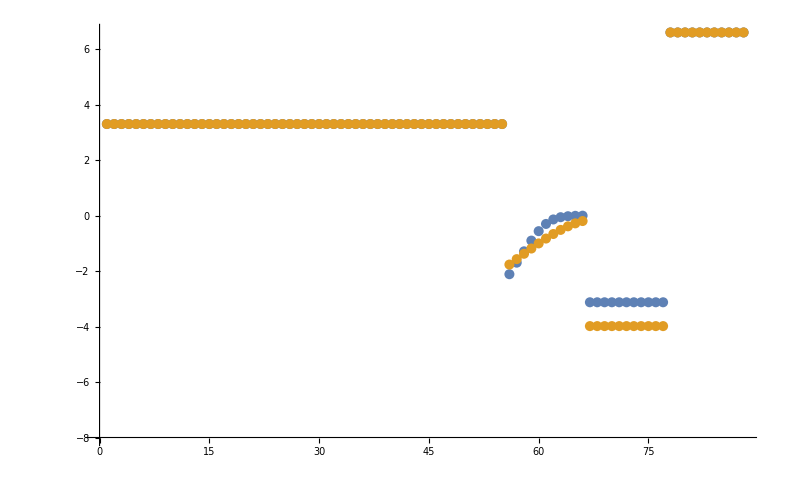

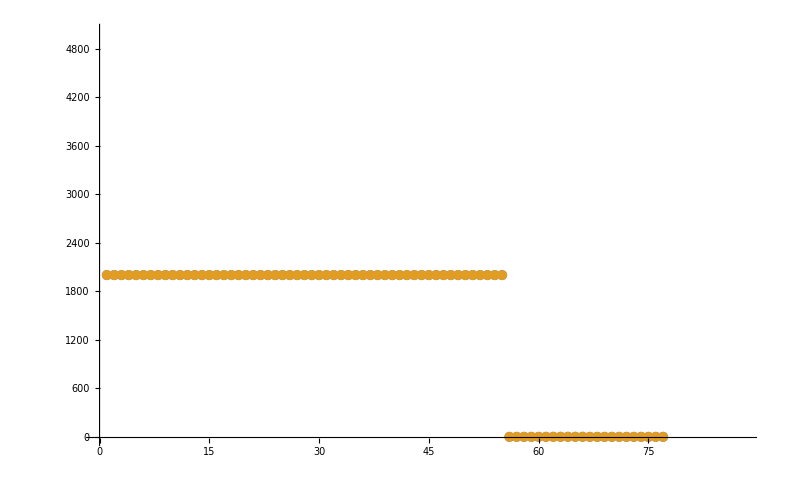

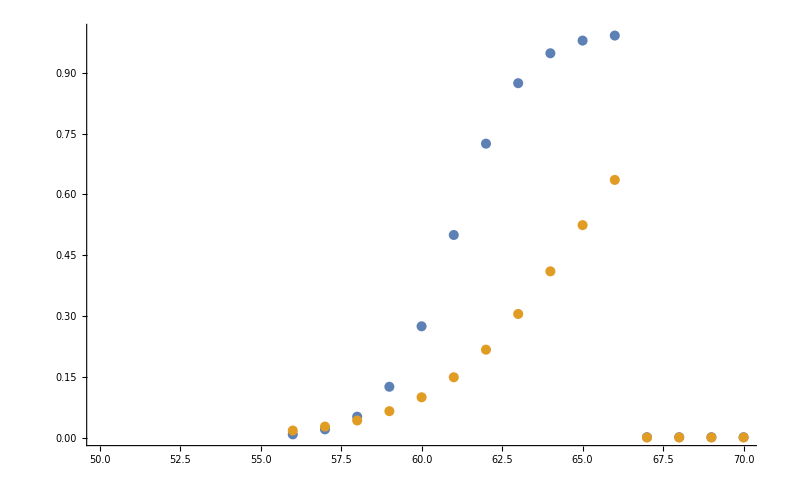

```mathematica
dataSet=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]], filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}, PlotRange->{{50,70}, {0,1}}]
```

### Parameter Distribution

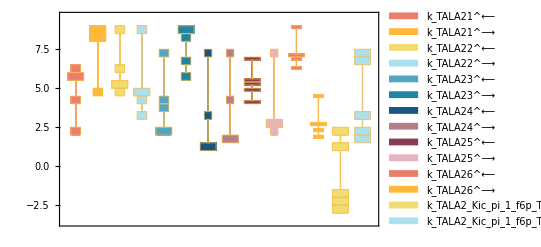

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

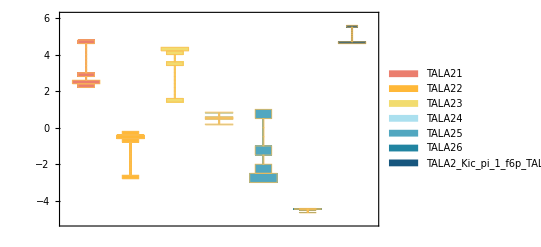

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

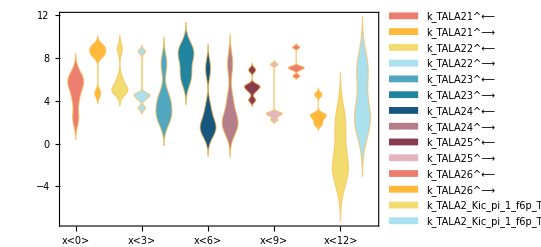

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

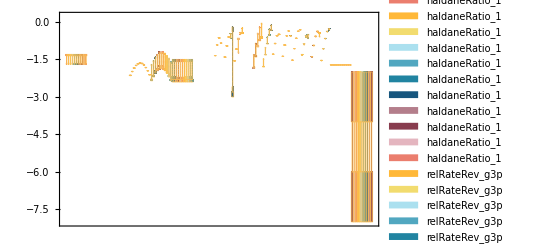

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138

```mathematica
backCalculateRatios[haldaneRatiosList[[2]][[1]], haldaneRatiosList[[2]][[2]], paramFitSub]//TableForm
```